# Analizando cuásares

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\ELXMA\Desktop\UV\REMONTADA\cata\4

Trabajaremos con datos de cuásares descubiertos a distintos redshifts. El propósito es analizarlos estadísticamente, ajustar una distribución conocida y ver si existe alguna correlación entre algunas variables

```mathematica
data=Import["astrostatistics.psu.edu_MSMA_datasets_SDSS_QSO.dat"]
```

{{SDSS,z,u_mag,sig_u_mag,g_mag,sig_g_mag,r_mag,sig_r_mag,i_mag,sig_i_mag,z_mag,sig_z_mag,FIRST,ROSAT,Mp},77428,{235959.44+000841.5,1.3553,21.012,0.113,7,0.15,0.,-9.,-24.064}}
 |  |  |  |

Ahora, lo primero que haremos para obtener una idea general de los datos que tenemos es intentar conocer cuales son los encabezados (o header) de la tabla, esto lo podemos hacer de la siguiente manera:

```mathematica
Do[Print[k," ",data[[1,k]]],{k,Length[data[[1]]]}]
```

1 SDSS

2 z

3 u_mag

4 sig_u_mag

5 g_mag

6 sig_g_mag

7 r_mag

8 sig_r_mag

9 i_mag

10 sig_i_mag

11 z_mag

12 sig_z_mag

13 FIRST

14 ROSAT

15 Mp

Ahora, conociendo ya el  header del archivo, intentaremos definir nuestras variables de interés. Para ello, lo que haremos será eliminar el Header, es decir, la primera fila, esto lo puede hacer la función Rest

```mathematica
data2=Rest[data]
```

{{000006.53+003055.2,1.8227,20.389,0.066,20.468,0.034,20.332,0.037,20.099,0.041,20.053,0.121,0.,-9.,-25.1},77427,{235959.44+000841.5,1.3553,21.012,0.113,20.892,6,0.15,0.,-9.,-24.064}}
 |  |  |  |

```mathematica
Length[data2]
```

77429

Ahora, con la función Select, seleccionaremos los valores que cumplan con que r_mag sea mayor a 15.0, y lo definiremos como aux3. Recordemos de los header que r_mag corresponde a la columna 7 de la matriz con datos.

```mathematica
data3=Select[data2,#[[7]]>15.0 &](* select r mag > 15. *)
```

{{000006.53+003055.2,1.8227,20.389,0.066,20.468,0.034,20.332,0.037,20.099,0.041,20.053,0.121,0.,-9.,-25.1},77293,{235959.44+000841.5,1.3553,21.012,0.113,20.892,6,0.15,0.,-9.,-24.064}}
 |  |  |  |

Por otro lado, definiremos aux4 como aquellos datos de aux3 que cumplan con que g_mag - es decir, la columna 5 de la matriz - sea mayor a 15.0,

```mathematica
data4=Select[data3,#[[5]]>15.0 &]; (* select g mag > 15. *)
```

Y finalmente, seleccionaremos los valores de aux4 que cumplan con que u_mag, es decir, la columna 3, sea mayor a 15.0, y la definiremos como la variable datos .

```mathematica
datos=Select[data4,#[[3]]>15.0 &];
```

```mathematica
Dimensions[datos]
```

{77292,15}

Donde

	•  r_mag: magnitud R (luminosidad en el filtro de banda R, captura luz en regiones cercana al rojo del espectro).
	
	•  g_mag: magnitud G (luminosidad en el filtro de banda G, que abarca parte del espectro visible).
	
	• u_mag:  magnitud U (luminosidad en el filtro de banda U, que captura luz ultravioleta cercana como cuásares).
	
Ahora, definiremos las siguiente variables

```mathematica
z=datos[[All,2]]; (* Redshift, columna 2 *)
u=datos[[All,3]]; (* u_mag, columna 3 *)
g=datos[[All,5]]; (* g_mag, columna 5 *)
r=datos[[All,7]] ; (* r_magcolumna 7 *)
```

Y nos aseguramos de que las dimensiones sean las mismas!

```mathematica
Dimensions[z]
```

{77292}

# Distribución de los datos y función moments

Ahora, lo que haremos será ver cómo se encuentran distribuidos los datos tanto para el redshift (z), magnitud U (u), magnitud G (g) y magnitud R (r). Para ello, podemos utilizar la función de Wolfram Histogram, la cual gráfica un histograma de los datos (ya sea z, u, g y r), lo que nos permite visualizar las distribuciones de frecuencias. Recordemos que en un histograma el eje x representa los valores de los datos y el eje y representa la intensidad, es decir, las frecuencias.

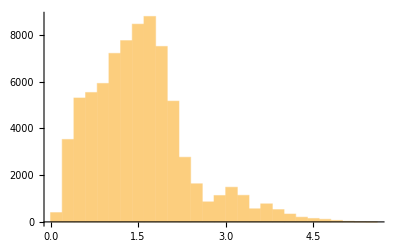

```mathematica
Histogram@z
```

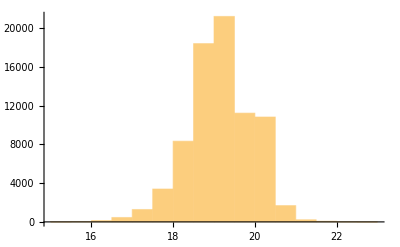

```mathematica
Histogram@r
```

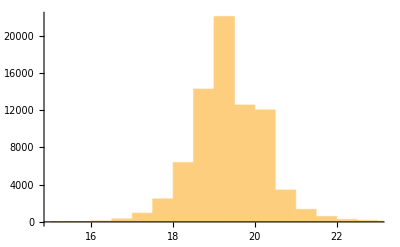

```mathematica
Histogram@g
```

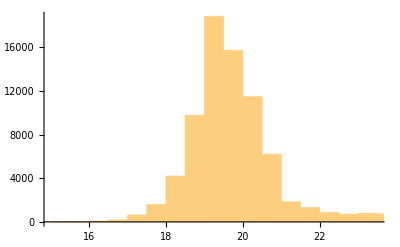

```mathematica
Histogram@u
```

### Momento de una distribución normal

Def. Son indicadores genéricos de una distribución, relacionadas con la forma de la gráfica de la función. Si la función representa la densidad de masa, entonces el momento cero es la masa total, el primer momento es el centro de masa y el segundo momento es el momento de inercia

Ahora, con la función de Wolfram: Moment, vamos a calcular los primeros cuatro momentos de una distribución normal  con parámetros μ y σ, donde 

	•  El momento de orden 1 es la media
	
	•  El momento de orden 2 es la varianza
	
	•  El momento de orden 3 es el sesgo o skewness, que proporciona información sobre la simetría de la
	   distribución tal que sesgo > 0 indica que la cola derecha de la distribución es más larga o pesada que
	    la izquierda.
	    
	    -Graphics-
	
	•  El momento de orden 4 es la curtosis, y mide la concentración de datos en las colas de la distribución.
	   Una curtosis alta indica que los datos tienen colas más pesadas y peaks más puntiagudos en comparación
	   con una distribución normal (gaussiana).
	   
	   -Graphics-

Éstas son útiles para caracterizar la forma y la tendencia central de la distribución gaussiana. 

Entonces, obtenemos los 4 momentos de una distribución normal, con esto buscamos obtener un histograma de una distribución normal, para poder ver si nuestros datos, z, u, g y r se ajustan o no a una distribución gaussiana.

```mathematica
Moment[NormalDistribution[μ,σ],#]&/@Range[4]
```

{μ,μ^2+σ^2,μ (μ^2+3 σ^2),μ^4+6 μ^2 σ^2+3 σ^4}

Ahora, calcularemos los 4 primeros momentos centrales de una distribución normal. Los momentos centrales son una variante de los momentos que tienen en cuenta la tendencia central de la distribución al centrarse en la diferencia entre los valores de los datos y la media de la distribución. Media 0

```mathematica
CentralMoment[NormalDistribution[μ,σ],#]&/@Range[4]
```

```mathematica
{0,σ^2,0,3 σ^4}
```

{0,σ^2,0,3 σ^4}

Ahora, generaremos una muestra aleatoria de un millón (10^6) valores a partir de una distribución normal, podemos ver como se distribuyen como la función Histogram.

```mathematica
zt = RandomVariate[NormalDistribution[],10^6];
```

Y podemos calcular los primeros cuatro momentos de la distribución y los primeros cuatro momentos centrales.

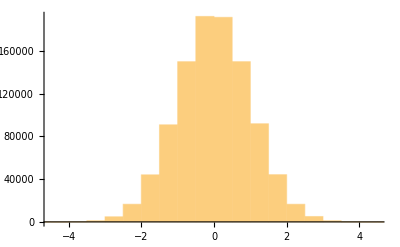

```mathematica
Histogram@zt
```

Y podemos calcular los primeros cuatro momentos de la distribución y los primeros cuatro momentos centrales.

```mathematica
Moment[zt,#] & /@ Range[4]
```

{0.00164617,0.998077,0.00567401,2.98853}

```mathematica
CentralMoment[zt,#]&/@Range[4]
```

{0.,0.998074,0.000744996,2.98851}

### Aplicación a nuestros datos!

Ahora crearemos un histograma suavizado con la función SMoothHistogram de los datos de redshift (z), esto para obtener una mejor visualización y más continua

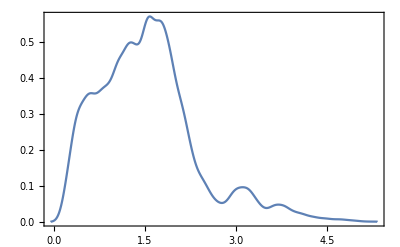

```mathematica
grSH=SmoothHistogram[z,Frame->True]
```

Y ahora obtenemos el momento y el momento central.

```mathematica
Moment[z,#] & /@ Range[2]
```

{1.53748,3.03929}

```mathematica
CentralMoment[z,#] & /@ Range[4]
```

{0.,0.675452,0.530335,1.95864}

### Distribución de Probabilidad: Ajuste a Distribución

Def. La función de densidad de probabilidad (PDF) es una función matemática que describe la distribución de probabilidad de una variable aleatoria continua. En otras palabras, muestra cómo se distribuyen las probabilidades de los diferentes valores que puede tomar una variable aleatoria en un rango específico. La forma de la PDF depende de la distribución de probabilidad que se esté modelando. Por ejemplo, la PDF de una distribución normal (gaussiana) tiene la forma de una campana, mientras que la PDF de una distribución exponencial tiene una forma decreciente exponencial. Cada distribución tiene su propia PDF característica que se utiliza para calcular probabilidades y realizar análisis estadísticos.

Debido a como son nuestros datos, crearemos un gráfico de densidad de probabilidad (PDF) para la distribución gamma con diferentes valores de parámetro α igual a 1, 4 y 6. El gráfico se crea en el rango de x de 0 a 20.

Recordemos que...

Def. La distribución gamma es una distribución de probabilidad continua que se utiliza comúnmente en estadísticas y teoría de probabilidad para modelar variables aleatorias positivas y asimétricas, como es nuestro caso para los datos de Redshift y tiene parámetros son parámetros

α:  Controla la forma de la distribución. Determina la asimetría y la inclinación de la cola de la distribución. A mayor α, la distribución gamma tiende a ser menos sesgada y más similar a una distribución normal. 

β: controla la dispersión De la distribución. A mayor β, la distribución gamma se estrecha y se concentra alrededor de su media.

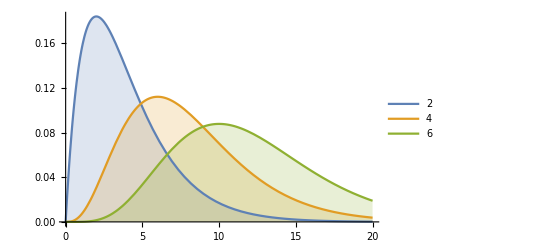

```mathematica
Plot[Table[PDF[GammaDistribution[α,2],x],{α,{2,4,6}}]//Evaluate,{x,0,20},Filling->Axis,PlotLegends->{2,4,6}]
```

Así confirmamos que a mayor α, la curva es más simétrica. Luego, haremos lo mismo pero en lugar de variar α, vamos a variar β.

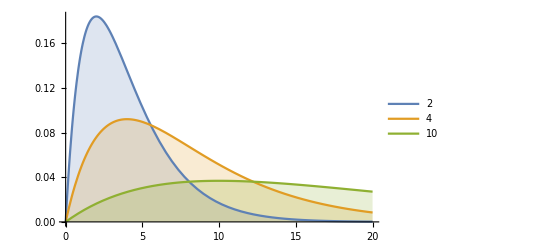

```mathematica
Plot[Table[PDF[GammaDistribution[2,β],x],{β,{2,4,10}}]//Evaluate,{x,0,20},Filling->Axis,PlotLegends->{2,4,10}]
```

Confirmamos que a mayor β, la distribución gamma se estrecha y se concentra alrededor de su media. Notemos la función de densidad de probabilidad para la distribución gamma es

```mathematica
PDF[GammaDistribution[α,β],x]
```

Piecewise[{{(ⅇ^(-x/β) x^(-1+α) β^-α)/Gamma[α], x>0}, {0, True}}]

### Aplicación a datos de redshift (z)

Ahora, definiremos meq, una variable que contiene dos ecuaciones, que establecen que los primeros dos momentos de la distribución de los datos del redshif (z) son iguales a los primeros dos momentos de la distribución gamma. Esto lo haremos con el propósito de ajustar nuestros datos a la función gamma.

```mathematica
Moment[GammaDistribution[α,β],#]&/@Range[2]
```

{α β,α (1+α) β^2}

```mathematica
meq=Table[Moment[z,k]==Moment[GammaDistribution[α,β],k],{k,1,2}]
```

{1.53748==α β,3.03929==α (1+α) β^2}

Y ocupamos la función NSolve para resolver el sistema de ecuaciones anterior, y así encontrar los valores de α y β que mejor se ajustan a los datos “z” en términos de los primeros dos momentos

```mathematica
NSolve[meq,{α,β}]
```

{{α→3.49964,β→0.439325}}

Ahora comparemos

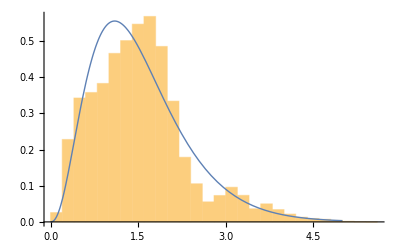

```mathematica
Show[Histogram[z,Automatic,"ProbabilityDensity"],Plot[Evaluate[PDF[GammaDistribution[α,β],x]/.%],{x,0,5},PlotStyle->Thick]]
```

### Función FindDistribution

La función FindDistribution encuentra las distribuciones que se ajustan mejor a nuestros datos con sus respectivos parámetros.

```mathematica
dists=FindDistribution[z,4]
```

{ExtremeValueDistribution[1.16135,0.657485],MixtureDistribution[{0.910212,0.089788},{NormalDistribution[1.34539,0.594996],NormalDistribution[3.46634,0.670695]}],MixtureDistribution[{0.714751,0.285249},{NormalDistribution[1.23783,0.570889],GammaDistribution[5.34335,0.42717]}],MixtureDistribution[{0.630379,0.369621},{NormalDistribution[1.10832,0.514525],LogNormalDistribution[0.759713,0.331395]}]}

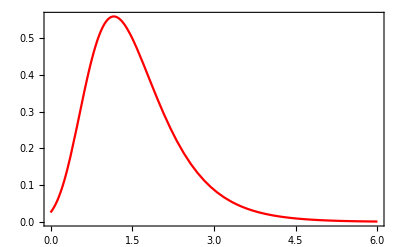

```mathematica
gr1=Plot[PDF[dists[[1]],x],{x,0,6},Frame->True,PlotStyle->Red]
```

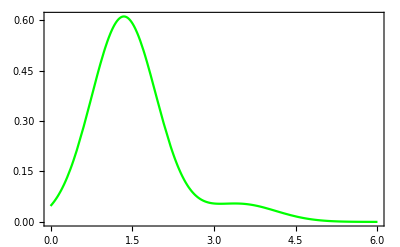

```mathematica
gr2=Plot[PDF[dists[[2]],x],{x,0,6},Frame->True,PlotStyle->Green]
```

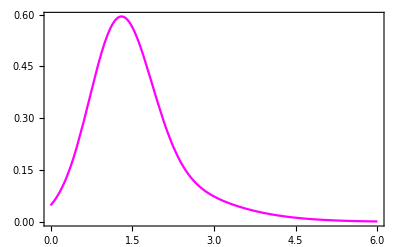

```mathematica
gr3=Plot[PDF[dists[[3]],x],{x,0,6},Frame->True,PlotStyle->Magenta]
```

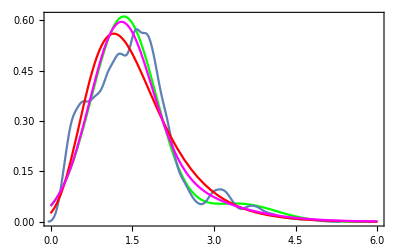

```mathematica
Show[gr2,grSH,gr1,gr3,PlotLegends->{2,4,10}]
```

### Correlaciones

Def. La correlación es una medida estadística que se utiliza para cuantificar la relación o asociación entre dos o más variables. 

Existen diferentes tipos de correlaciones, pero las dos más comunes son:

1. Correlación Lineal:

   -  Usa para medir la relación lineal entre dos variables numéricas.
   -  r ~ 1 indica una correlación positiva fuerte, lo que significa que a medida que una variable aumenta, la otra también tiende a aumentar en una relación lineal.
   -  r ~ -1 indica una correlación negativa fuerte, lo que significa que a medida que una variable aumenta, la otra tiende a disminuir en una relación lineal.
   -  r ~ 0 indica una correlación débil o nula, lo que significa que no hay una relación lineal aparente entre las variables.

2. Correlación No Lineal:

   - La correlación no lineal se utiliza cuando la relación entre dos variables no sigue una relación lineal.
   - Pueden existir relaciones no lineales, como exponenciales, logarítmicas o polinómicas, que no pueden ser capturadas adecuadamente por el coeficiente de correlación de Pearson.

## Análisis de correlaciones

#### Correlación entre el redshift y mag en banda R

Definimos la nueva variable datos2, que contiene los pares de datos {redshift, Mag en banda R}

```mathematica
datos2=Transpose[{datos[[All,2]],datos[[All,7]]}];
```

```mathematica
Length[datos2]
```

77292

Con la función ListPlot, podemos graficar los pares de datos definidos antes, para poder visualizar si existe o no correlación entre las dos variables.

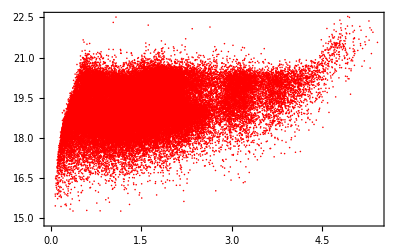

```mathematica
ListPlot[datos2,Frame->True,PlotRange->All,PlotStyle->Red]
```

Luego, podemos obtener el coeficiente de correlación de Pearson con la función Correlation.

```mathematica
Correlation[datos[[All,2]],datos[[All,7]]]
```

0.31916

```mathematica
Correlation[z,r]
```

0.31916

Notemos que, como acá hay un sesgo de selección, pues hemos definido datos como u_mag, r_mag, g_mag > 15. Por lo mismo, no hay correlación en este caso.

#### Correlación entre Redshift y Mag en banda U

```mathematica
datos2=Transpose[{z,u}];
```

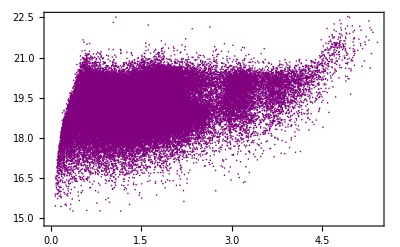

0.634705

```mathematica
ListPlot[datos2,Frame->True,PlotRange->All,PlotStyle->Purple]
Correlation[z,u]
```

### Correlación entre Redshift y Mag en banda G

```mathematica
datos2=Transpose[{z,g}];
```

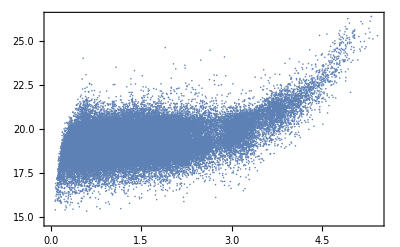

0.440343

```mathematica
ListPlot[datos2,Frame->True,PlotRange->All]
Correlation[z,g]
```

### Correlación entre Mag en banda-G y Mag en banda - R

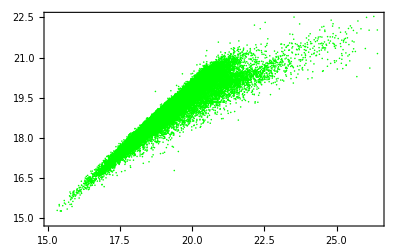

0.932272

```mathematica
datos2=Transpose[{g,r}]; 
ListPlot[datos2,Frame->True,PlotRange->All,PlotStyle->Green]
Correlation[g,r]
```

Correlación entre Conjuntos de datos que siguen una Distribución Bivariante Normal para diferentes Coeficientes

Def. Una distribución binormal es una distribución de probabilidad que describe conjuntamente dos variables aleatorias continuas. Es una generalización de la distribución normal univariante a dos dimensiones por lo que asume que las dos variables aleatorias siguen una distribución normal en sí mismas y que pueden estar correlacionadas.

Ahora, lo que intentaremos hacer es  generar, visualizar y calcular coeficientes de correlación para conjuntos de datos que siguen una distribución binormal. 

Lo primero que haremos, será generar un gráfico usando la función ListPlot que muestre 3000 puntos generados aleatoriamente a partir de una distribución bivariante normal con un coeficiente de correlación de 0.5.

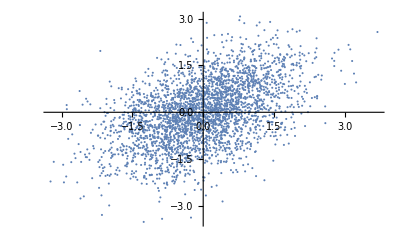

```mathematica
ListPlot[RandomVariate[BinormalDistribution[0.5],3000]] (* BinormalDistribution[ρ] is a bivariate normal distribution (2D Gaussian) with μ=0, σ=1 and covariance matrix {{1,ρ},{ρ,1}}; RandomVariate gives a list of 3000 points from the BinormalDistribution *)
```

Luego, crearemos una lista llamada data que contiene varios conjuntos de datos generados a partir de la distribución binormal con diferentes valores de coeficiente de correlación: -0.99, -0.75, -0.25, -0.5, 0.0, 0.25, 0.5, 0.75 y 0.99. La función “SeedRandom” se utiliza para asegurarse de que los conjuntos de datos generados sean reproducibles. Luego vamos a graficar 
la dispersión para el séptimo conjunto de datos en la lista “data” correspondiente a . El quinto conjunto de datos corresponde a un valor del coeficiente de 0.5, igual al ejemplo anterior.

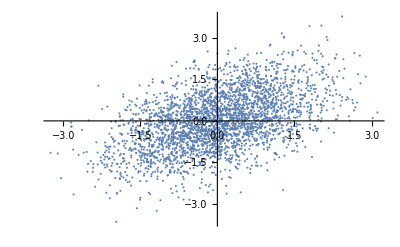

```mathematica
data=BlockRandom[SeedRandom[1];
Table[RandomVariate[BinormalDistribution[i],3000],{i,{-.99,-.75,-.25,-.5,0.,.25,.5,.75,.99}}]];
ListPlot[data[[7]]]
```

Con esta información, podemos calcular el coeficiente de correlación de Pearson para el segundo conjunto de datos en la lista “data”. El resultado es el coeficiente de correlación entre las dos variables en ese conjunto de datos. Notemos que al poner [[1, 2]], nos permite especificar que entregue el coeficiente de correlación entre la primera variable (definida aleatoriamente) y la segunda variable en el conjunto de datos.

```mathematica
Correlation[data[[2]]][[1,2]]
```

-0.740416

Por otro lado, si no especificamos, podemos obtener la matriz de correlación que muestra los coeficientes de correlación entre todas las combinaciones posibles de variables en el conjunto de datos, es decir, entre la primera variable con la primera variable, la priemra con la segunda, la segunda con la primera y la segunda consigo misma.

```mathematica
Correlation[data[[2]]]//MatrixForm
```

(1. | -0.740416
-0.740416 | 1.)

Y, para tener una mejor visualización de como se correlacionan los datos que siguen una distribución normal, y que presentan diferentes coeficientes de correlación, podemos crear una cuadrícula de gráficos de dispersión para todos los conjuntos de datos en “data”, organizados en filas y columnas.

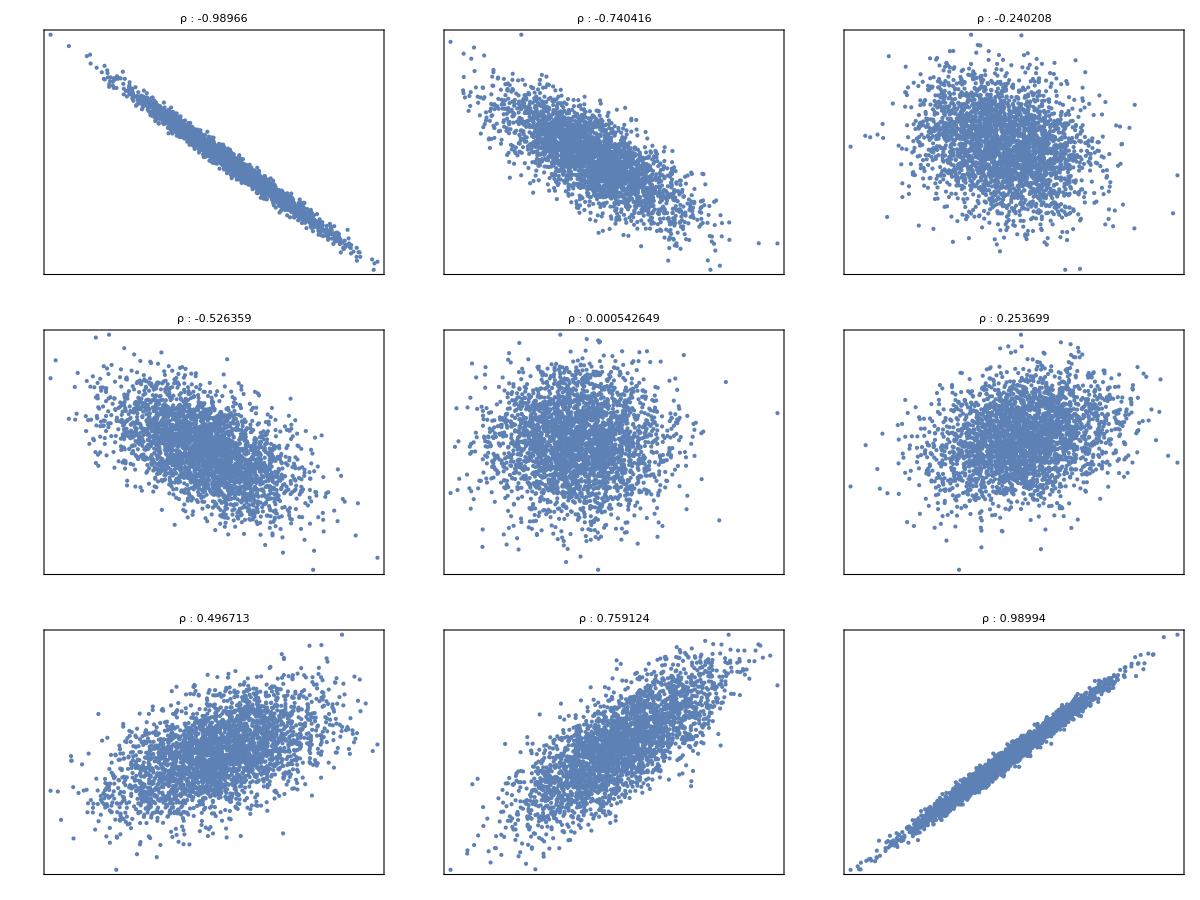

```mathematica
Grid[Partition[Table[ListPlot[i,PlotStyle->Directive[PointSize[Tiny]],FrameTicks->None,Frame->True,Axes->None,PlotLabel->Row[{"ρ : ",Correlation[i][[1,2]]}]],{i,data}],3]]
```

## Covarianza

Otra medida bastante útil para saber si dos variables se relacionan entre sí, es la covarianza. La covarianza es una medida estadística que describe la relación entre dos variables aleatorias y cómo varían juntas, es decir, cuantifica la tendencia conjunta de dos variables a aumentar o disminuir al mismo tiempo. Si la covarianza es positiva, indica que cuando una variable aumenta, la otra tiende a aumentar. Si la covarianza es negativa, indica que cuando una variable aumenta, la otra tiende a disminuir. Si la covarianza es cercana a cero, indica que no hay una relación clara entre las dos variables.

Ahora, generaremos datos aleatorios, para calcular su matriz de covarianza y luego crear una visualización de la matriz de covarianza. Para ello, primero crearemos la matriz de datos aleatorios data, con dimensiones  20x5 utilizando la función RandomReal, es decir, cada elemento de la matriz es un número real generado aleatoriamente en el rango de 0 a 10. En total tendremos 5 variables (columnas) con 20 datos cada una.

```mathematica
data=RandomReal[10,{20,5}]; 
Dimensions[data]
```

{20,5}

Luego, vamos a obtener la matriz de covarianza de la matriz anterior. Para esto, podemos utilizar la función Covariance. Notemos que esta matriz muestra las covarianzas entre todas las combinaciones posibles de las 5 variables en el conjunto de datos .

```mathematica
Covariance[data]//MatrixForm
```

(11.1802 | 1.87586 | 0.289035 | -3.12824 | 3.14197
1.87586 | 7.85542 | -2.41868 | -0.696373 | 0.00988158
0.289035 | -2.41868 | 7.71463 | 1.61904 | 1.00868
-3.12824 | -0.696373 | 1.61904 | 8.45196 | 1.18671
3.14197 | 0.00988158 | 1.00868 | 1.18671 | 7.37915)

Ahora, para poder obtener una mejor visualización de la matriz de covarianza, podemos usar la función ArrayPlot, en donde los valores en la matriz de covarianza se representan gráficamente mediante colores . Cada celda de la trama de matriz corresponde a la covarianza entre dos variables . Los colores y tonos en la trama proporcionan una representación visual de la magnitud y el signo de las covarianzas .

```mathematica
ArrayPlot[Covariance[data],PlotLegends->Automatic,ImageSize->300]
```

-Graphics-

#### ¿Diagonal de Matriz Covarianza y Varianza?

```mathematica
Diagonal[Covariance[data]]
```

{11.1802,7.85542,7.71463,8.45196,7.37915}

```mathematica
Variance[data]
```

{11.1802,7.85542,7.71463,8.45196,7.37915}

Podemos notar que la diagonal de la matriz de covarianza de ciertos datos es igual a la varianza de los datos! Esto ocurre porque la covarianza de una variable con ella misma es igual a su propia varianza.

### Covarianza para nuestros datos!

```mathematica
datos3=Transpose[{z,u,g,r}];
```

```mathematica
ArrayPlot[Covariance[datos3],PlotLegends->Automatic]
```

-Graphics-

```mathematica
Diagonal[Covariance[datos3]]
```

{0.675461,1.92758,0.82254,0.61085}

```mathematica
Variance[datos3]
```

{0.675461,1.92758,0.82254,0.61085}